# PairAlignedDynamics

## First-harmonic rescaled dynamics and canonical pair-plane alignment

## Purpose

This notebook supports Chapter 3. It constructs the pair-aligned rescaled operator R_α, verifies the canonical alignment of a nondegenerate first harmonic, checks that the first-harmonic component is fixed, and illustrates exponential convergence of the complementary modes.

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Fourier and averaging definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

fourierCoefficients[p_List] := Module[{F},
  F = fourierMatrix[Length[p]];
  ConjugateTranspose[F] . N[p]
];

fourierSynthesis[c_List] :=
  fourierMatrix[Length[c]] . c;

centerPolygon[p_List] :=
  N[p] - Mean[N[p]];

applyA[p_List, alpha_?NumericQ] :=
  (1 - alpha) N[p] + alpha RotateLeft[N[p]];

lambda[n_Integer?Positive, k_Integer, alpha_?NumericQ] :=
  (1 - alpha) + alpha Exp[2 Pi I k/n];

mu[n_Integer?Positive, k_Integer, alpha_?NumericQ] :=
  Abs[lambda[n, k, alpha]];
```

The averaging operator satisfies

A_α(φ⃗)_k=λ_k(φ⃗)_k

```mathematica
nExample = 12;
alphaExample = 0.35;
```

## 2. First-harmonic decomposition

```mathematica
pairPlaneCoefficients[p_List] := Module[{n, c, result},
  n = Length[p];
  c = fourierCoefficients[p];
  result = ConstantArray[0, n];
  result[[2]] = c[[2]];
  result[[n]] = c[[n]];
  result
];

pairPlaneProjection[p_List] :=
  fourierSynthesis[pairPlaneCoefficients[p]];

perpendicularProjection[p_List] :=
  N[p] - pairPlaneProjection[p];

firstHarmonicData[p_List] := Module[{n, c},
  n = Length[p];
  c = fourierCoefficients[p];
  <|
    "c1" -> c[[2]],
    "cNMinus1" -> c[[n]]
  |>
];
```

```mathematica
SeedRandom[3030];
pExample = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
pExample = centerPolygon[pExample];
pPair = pairPlaneProjection[pExample];
pPerp = perpendicularProjection[pExample];
decompositionError = Norm[N[pExample - pPair - pPerp]];
decompositionQ = decompositionError < 10^-10;
```

```mathematica
decompositionError
```

1.66533×10^-16

```mathematica
decompositionQ
```

True

## 3. Alignment parameters

For

p_(±1)=c_1 φ_1+c_(n-1)φ_(n-1)

Chapter 3 defines the rotation parameter ξ=e^(i(θ_1+θ_(n-1))/2) and the anisotropy parameter

r=(|c_1|+|c_(n-1)|)/(|c_1|-|c_(n-1)|)

```mathematica
alignmentParameters[p_List] := Module[
  {data, c1, cN, theta1, thetaN, denominator},
  data = firstHarmonicData[p];
  c1 = data["c1"];
  cN = data["cNMinus1"];
  denominator = Abs[c1] - Abs[cN];
  If[Abs[N[denominator]] < 10^-12,
    Return[Missing["DegenerateFirstHarmonic"]]
  ];
  theta1 = Arg[c1];
  thetaN = Arg[cN];
  <|
    "Xi" -> Exp[I (theta1 + thetaN)/2],
    "R" -> (Abs[c1] + Abs[cN])/denominator,
    "ThetaMinus" -> (theta1 - thetaN)/2,
    "AlignedAmplitude" -> (Abs[c1] + Abs[cN]) Exp[I (theta1 - thetaN)/2]
  |>
];
```

```mathematica
paramsExample = alignmentParameters[pExample];
paramsExample
```

<|Xi→0.979686-0.200539 ⅈ,R→5.45819,ThetaMinus→-2.66683,AlignedAmplitude→-0.684481-0.351801 ⅈ|>

## 4. Real-linear dilation

D_r(z)=((1+r)z+(1-r)z̄)/2=u+irv

```mathematica
dilationD[z_, r_?NumericQ] :=
  ((1 + r) z + (1 - r) Conjugate[z])/2;

inverseDilationD[z_, r_?NumericQ] :=
  dilationD[z, 1/r];
```

```mathematica
zTest = 0.7 - 1.2 I;
rTest = 2.3;
dilationInverseError = Abs[N[inverseDilationD[dilationD[zTest, rTest], rTest] - zTest]];
dilationInverseQ = dilationInverseError < 10^-10;
```

```mathematica
dilationInverseError
```

2.22045×10^-16

```mathematica
dilationInverseQ
```

True

## 5. The normalizing maps H and H inverse

H=D_r∘ξ̄, H^-1=ξ∘D_(1/r)

```mathematica
applyH[p_List, params_Association] := Module[{xi, r},
  xi = params["Xi"];
  r = params["R"];
  dilationD[Conjugate[xi] N[p], r]
];

applyHInverse[p_List, params_Association] := Module[{xi, r},
  xi = params["Xi"];
  r = params["R"];
  xi inverseDilationD[N[p], r]
];
```

```mathematica
hInverseError = Norm[N[applyHInverse[applyH[pExample, paramsExample], paramsExample] - pExample]];
hInverseQ = hInverseError < 10^-10;
```

```mathematica
hInverseError
```

9.61506×10^-16

```mathematica
hInverseQ
```

True

## 6. Alignment of the first harmonic

The alignment lemma states

H p_(±1)=a' φ_1

```mathematica
alignedPair = applyH[pPair, paramsExample];
alignedPairCoefficients = fourierCoefficients[alignedPair];
alignedTarget = paramsExample["AlignedAmplitude"] fourierVector[nExample, 1];
alignmentError = Norm[N[alignedPair - alignedTarget]];
alignmentQ = alignmentError < 10^-10;
```

```mathematica
alignedPairCoefficients
```

{-1.38778×10^-17-2.64545×10^-17 ⅈ,-0.684481-0.351801 ⅈ,2.77556×10^-17+4.16334×10^-17 ⅈ,-4.29344×10^-17+1.38778×10^-17 ⅈ,-3.46945×10^-18+2.08167×10^-17 ⅈ,1.38778×10^-17+6.93889×10^-17 ⅈ,-2.77556×10^-17-4.29344×10^-17 ⅈ,5.55112×10^-17+3.81639×10^-17 ⅈ,2.77556×10^-17+2.08167×10^-17 ⅈ,3.59955×10^-17-4.16334×10^-17 ⅈ,3.46945×10^-18+1.38778×10^-17 ⅈ,2.63678×10^-16+1.80411×10^-16 ⅈ}

```mathematica
alignmentError
```

5.1675×10^-16

```mathematica
alignmentQ
```

True

## 7. Spectral rescaling

Define

OverTilde[A_α]=A_α/λ_1

```mathematica
applyATilde[p_List, alpha_?NumericQ] := Module[{n},
  n = Length[p];
  applyA[p, alpha]/lambda[n, 1, alpha]
];
```

```mathematica
phi1 = fourierVector[nExample, 1];
aTildeFixError = Norm[N[applyATilde[phi1, alphaExample] - phi1]];
aTildeFixQ = aTildeFixError < 10^-10;
```

```mathematica
aTildeFixError
```

1.5899×10^-16

```mathematica
aTildeFixQ
```

True

## 8. Pair-aligned rescaled operator

R_α=H^-1 OverTilde[A_α]H

```mathematica
applyR[p_List, alpha_?NumericQ, params_Association] :=
  applyHInverse[
    applyATilde[applyH[p, params], alpha],
    params
  ];

iterateR[p_List, alpha_?NumericQ, params_Association, m_Integer?NonNegative] :=
  Nest[applyR[#, alpha, params] &, N[p], m];
```

```mathematica
fixedPairError = Norm[N[applyR[pPair, alphaExample, paramsExample] - pPair]];
fixedPairQ = fixedPairError < 10^-10;
```

```mathematica
fixedPairError
```

1.01685×10^-16

```mathematica
fixedPairQ
```

True

## 9. Real linearity

```mathematica
SeedRandom[3131];
uTest = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
vTest = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
aTest = 1.7;
bTest = -0.6;
realLinearityError = Norm[N[
  applyR[aTest uTest + bTest vTest, alphaExample, paramsExample] -
  aTest applyR[uTest, alphaExample, paramsExample] -
  bTest applyR[vTest, alphaExample, paramsExample]
]];
realLinearityQ = realLinearityError < 10^-10;
```

```mathematica
realLinearityError
```

1.86107×10^-15

```mathematica
realLinearityQ
```

True

## 10. Contraction on the complementary subspace

ρ̂=max_(2≤j≤n-2)μ_j/μ_1<1

```mathematica
rhoHat[n_Integer?Positive, alpha_?NumericQ] :=
  Max@Table[mu[n, j, alpha]/mu[n, 1, alpha], {j, 2, n - 2}];

perpendicularDecay[p_List, alpha_?NumericQ, params_Association, m_Integer?NonNegative] :=
  Norm[perpendicularProjection[iterateR[p, alpha, params, m]]];
```

```mathematica
rhoExample = rhoHat[nExample, alphaExample];
decayTable = Table[
  {m, perpendicularDecay[pExample, alphaExample, paramsExample, m]},
  {m, 0, 40, 4}
];
{rhoExample, decayTable}
```

{0.906999,{{0,2.77813},{4,2.75014},{8,1.4778},{12,0.664484},{16,0.246057},{20,0.0713503},{24,0.136282},{28,0.122205},{32,0.0641094},{36,0.0149071},{40,0.0222009}}}

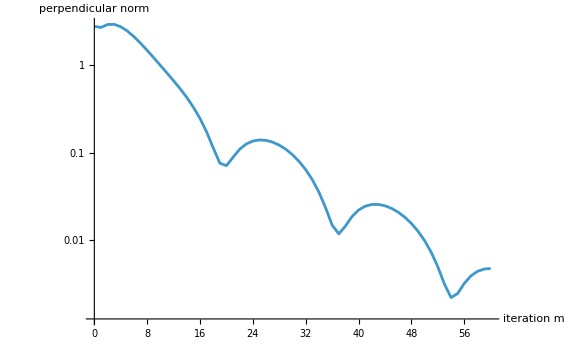

```mathematica
ListLogPlot[
  Table[
    {m, perpendicularDecay[pExample, alphaExample, paramsExample, m]},
    {m, 0, 60}
  ],
  Joined -> True,
  AxesLabel -> {"iteration m", "perpendicular norm"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 11. Convergence to the initial first harmonic

lim_(m→∞) R_α^m p=p_(±1)

```mathematica
limitError[p_List, alpha_?NumericQ, params_Association, m_Integer?NonNegative] :=
  Norm[N[iterateR[p, alpha, params, m] - pairPlaneProjection[p]]];

limitTable = Table[
  {m, limitError[pExample, alphaExample, paramsExample, m]},
  {m, 0, 60, 5}
];
limitTable // TableForm
```

0 | 2.77813
5 | 2.45638
10 | 0.995465
15 | 0.331067
20 | 0.0713503
25 | 0.140216
30 | 0.0949748
35 | 0.0236284
40 | 0.0222009
45 | 0.0231716
50 | 0.0098982
55 | 0.00247532
60 | 0.00476917

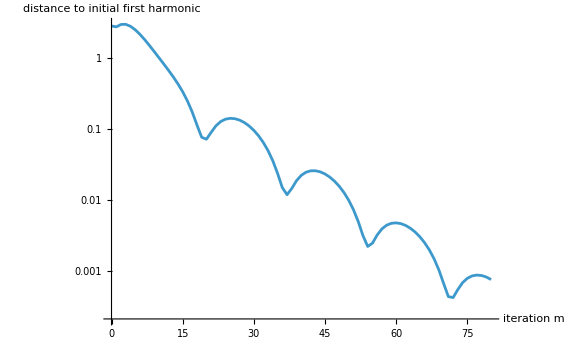

```mathematica
ListLogPlot[
  Table[
    {m, limitError[pExample, alphaExample, paramsExample, m]},
    {m, 0, 80}
  ],
  Joined -> True,
  AxesLabel -> {"iteration m", "distance to initial first harmonic"},
  PlotRange -> All,
  ImageSize -> Large
]
```

## 12. Elliptic limit geometry

The limiting first harmonic has semi-axis lengths

a=|c_1|+|c_(n-1)|, b=||c_1|-|c_(n-1)||

```mathematica
ellipseSemiAxes[p_List] := Module[{data, c1, cN},
  data = firstHarmonicData[p];
  c1 = data["c1"];
  cN = data["cNMinus1"];
  {Abs[c1] + Abs[cN], Abs[Abs[c1] - Abs[cN]]}
];

ellipseSemiAxes[pExample]
```

{0.769596,0.140998}

## 13. Polygon visualization

```mathematica
polygonPoints[p_List] :=
  N@Transpose[{Re[N[p]], Im[N[p]]}];

polygonPlot[p_List, title_] := Module[{pts},
  pts = polygonPoints[p];
  Graphics[
    {
      Thick,
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    },
    Axes -> True,
    AspectRatio -> 1,
    PlotRange -> All,
    PlotLabel -> title,
    ImageSize -> Large
  ]
];
```

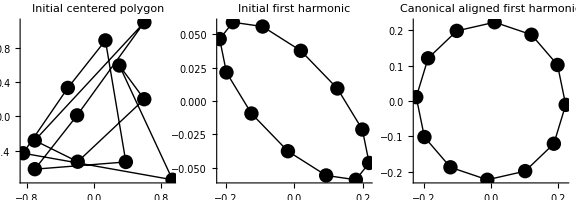

```mathematica
GraphicsRow[
  {
    polygonPlot[pExample, "Initial centered polygon"],
    polygonPlot[pPair, "Initial first harmonic"],
    polygonPlot[alignedPair, "Canonical aligned first harmonic"]
  },
  ImageSize -> Large
]
```

## 14. Pair-aligned evolution gallery

```mathematica
galleryTimes = {0, 1, 2, 5, 10, 20, 40};
galleryPolygons = Table[
  iterateR[pExample, alphaExample, paramsExample, m],
  {m, galleryTimes}
];
```

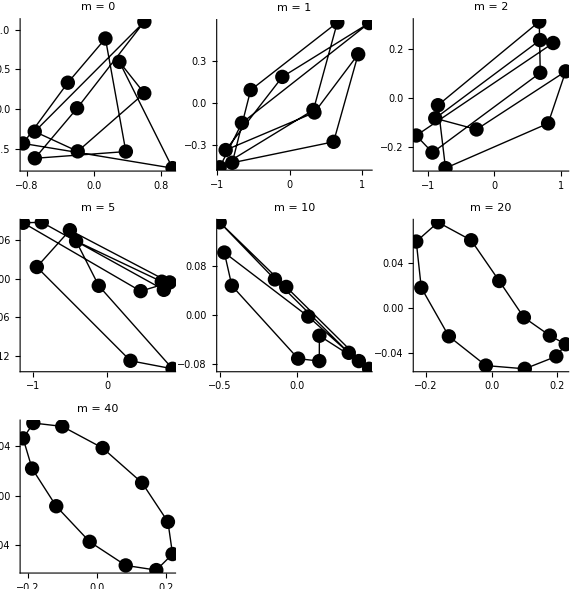

```mathematica
GraphicsGrid[
  Partition[
    MapThread[
      polygonPlot[#1, Row[{"m = ", #2}]] &,
      {galleryPolygons, galleryTimes}
    ],
    3,
    3,
    {1, 1},
    Nothing
  ],
  ImageSize -> Large
]
```

## 15. Independence of the limiting shape from alpha

```mathematica
alphaValues = {0.2, 0.35, 0.6, 0.8};
alphaLimitErrors = Table[
  {
    alpha,
    limitError[pExample, alpha, paramsExample, 80]
  },
  {alpha, alphaValues}
];
alphaLimitErrors // TableForm
```

0.2 | 0.0101287
0.35 | 0.000762708
0.6 | 0.000168194
0.8 | 0.0096654

## 16. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[18];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[
      {alpha, p, data, params, pair, hError, alignError, fixedError, linearError, limitErr, u, v},
      alpha = 0.37;
      SeedRandom[5000 + n];
      p = RandomReal[{-1, 1}, n] + I RandomReal[{-1, 1}, n];
      p = centerPolygon[p];
      data = firstHarmonicData[p];
      If[Abs[Abs[data["c1"]] - Abs[data["cNMinus1"]]] < 10^-6,
        p = p + 0.1 fourierVector[n, 1]
      ];
      params = alignmentParameters[p];
      pair = pairPlaneProjection[p];
      hError = Norm[N[applyHInverse[applyH[p, params], params] - p]];
      alignError = Norm[N[
        applyH[pair, params] -
        params["AlignedAmplitude"] fourierVector[n, 1]
      ]];
      fixedError = Norm[N[applyR[pair, alpha, params] - pair]];
      u = RandomReal[{-1, 1}, n] + I RandomReal[{-1, 1}, n];
      v = RandomReal[{-1, 1}, n] + I RandomReal[{-1, 1}, n];
      linearError = Norm[N[
        applyR[1.3 u - 0.4 v, alpha, params] -
        1.3 applyR[u, alpha, params] +
        0.4 applyR[v, alpha, params]
      ]];
      limitErr = limitError[p, alpha, params, 100];
      <|
        "n" -> n,
        "H inverse property" -> TrueQ[hError < 10^-9],
        "First-harmonic alignment" -> TrueQ[alignError < 10^-9],
        "First harmonic fixed" -> TrueQ[fixedError < 10^-9],
        "Real linearity" -> TrueQ[linearError < 10^-9],
        "Convergence at m=100" -> TrueQ[limitErr < 10^-5]
      |>
    ],
    {n, 5, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
verificationReport[]
```

## Conclusion

The notebook implements the Chapter 3 pair-aligned rescaling. The map H sends the initial nondegenerate first harmonic to a canonical pure first mode, the normalized averaging map fixes that mode, and the conjugated operator R_α fixes the original first-harmonic component while contracting all complementary modes. Its iterates therefore converge to the ellipse determined by the initial coefficients c_1 and c_(n-1).